```mathematica
Solve[{x^2+y^2==(k/a)^2,(x-l)^2+y^2==k^2},{y,x}]
```

{{y→-(√(-k^4+2 a^2 k^4-a^4 k^4+2 a^2 k^2 l^2+2 a^4 k^2 l^2-a^4 l^4))/(2 a^2 l),x→(k^2-a^2 k^2+a^2 l^2)/(2 a^2 l)},{y→(√(-k^4+2 a^2 k^4-a^4 k^4+2 a^2 k^2 l^2+2 a^4 k^2 l^2-a^4 l^4))/(2 a^2 l),x→(k^2-a^2 k^2+a^2 l^2)/(2 a^2 l)}}

```mathematica
%12/.Rule->Equal
```

{{y==-(√(-k^4+2 a^2 k^4-a^4 k^4+2 a^2 k^2 l^2+2 a^4 k^2 l^2-a^4 l^4))/(2 a^2 l),x==(k^2-a^2 k^2+a^2 l^2)/(2 a^2 l)},{y==(√(-k^4+2 a^2 k^4-a^4 k^4+2 a^2 k^2 l^2+2 a^4 k^2 l^2-a^4 l^4))/(2 a^2 l),x==(k^2-a^2 k^2+a^2 l^2)/(2 a^2 l)}}

```mathematica
Eliminate[{y==-(√(-k^4+2 a^2 k^4-a^4 k^4+2 a^2 k^2 l^2+2 a^4 k^2 l^2-a^4 l^4))/(2 a^2 l),x==(k^2-a^2 k^2+a^2 l^2)/(2 a^2 l)},k]
```

-(2 l x)/a+(1/a-a) x^2==-l^2/a-y^2/a+a y^2&&2 l x+(-1+a^2) x^2==l^2+y^2-a^2 y^2&&a≠0&&l≠0

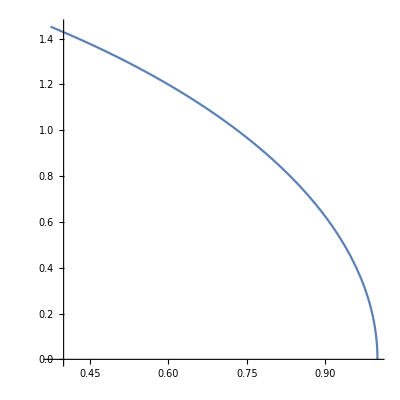

```mathematica
ParametricPlot[{1/8 (12-k^2),1/8 √(-144+40 k^2-k^4//Factor)},{k,2,3},AspectRatio->1]
```

```mathematica
Eliminate[{x^2+y^2+z^2==(k/a)^2,x^2+y^2+(z-m)^2==k^2},k]
```

```mathematica
Solve[m^2-2 m z==-x^2+a^2 x^2-y^2+a^2 y^2-z^2+a^2 z^2,z]
```

{{z→(-2 m-√(4 m^2-4 (1-a^2) (m^2+x^2-a^2 x^2+y^2-a^2 y^2)))/(2 (-1+a^2))},{z→(-2 m+√(4 m^2-4 (1-a^2) (m^2+x^2-a^2 x^2+y^2-a^2 y^2)))/(2 (-1+a^2))}}

```mathematica
Solve[m^2-2 m y==-x^2+a^2 x^2-y^2+a^2 y^2,y]
```

{{y→(-m-√(a^2 m^2-x^2+2 a^2 x^2-a^4 x^2))/(-1+a^2)},{y→(-m+√(a^2 m^2-x^2+2 a^2 x^2-a^4 x^2))/(-1+a^2)}}

```mathematica
Solve[l^2-2 l x==-x^2+a^2 x^2-y^2+a^2 y^2-z^2+a^2 z^2,z]
```

{{z→-(√(l^2-2 l x+x^2-a^2 x^2+y^2-a^2 y^2))/(√(-1+a^2))},{z→(√(l^2-2 l x+x^2-a^2 x^2+y^2-a^2 y^2))/(√(-1+a^2))}}

```mathematica
Solve[l^2-2 l x==-x^2+a^2 x^2-y^2+a^2 y^2,y]
```

{{y→-(√(l^2-2 l x+x^2-a^2 x^2))/(√(-1+a^2))},{y→(√(l^2-2 l x+x^2-a^2 x^2))/(√(-1+a^2))}}

```mathematica
Solve[{x^2+y^2==(3/2)^2,(x-3)^2+y^2==3^2},{y,x}]
```

```mathematica
{{y->-(3 √15)/8,x->3/8},{y->(3 √15)/8,x->3/8}}//N
```

{{y→-1.45237,x→0.375},{y→1.45237,x→0.375}}

```mathematica
ParametricPlot[(Solve[{x^2+y^2==(k/2)^2,(x-3)^2+y^2==k^2},{x,y}]/.Rule->Equal)[[1]],{k,3,4}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

-Graphics-

```mathematica
{{y->-1/8 √(-144+40 k^2-k^4),x->1/8 (12-k^2)},{y->1/8 √(-144+40 k^2-k^4),x->1/8 (12-k^2)}}/.Rule->Equal
```

{{y==-1/8 √(-144+40 k^2-k^4),x==1/8 (12-k^2)},{y==1/8 √(-144+40 k^2-k^4),x==1/8 (12-k^2)}}

```mathematica
(Solve[{x^2+y^2==(k/2)^2,(x-3)^2+y^2==k^2},{y,x}]/.Rule->Equal)[[1]]
```

```mathematica
{-1/8 √(-144+40 k^2-k^4),x==1/8 (12-k^2)}
```

```mathematica
ParametricPlot[(Solve[{x^2+y^2==(k/2)^2,(x-3)^2+y^2==k^2},{x,y}]/.Rule->Equal)[[1]],{k,3,4}]
```

```mathematica
Solve[{x^2+y^2==(k/2)^2,(x-3)^2+y^2==k^2},{x,y}]/.Rule->Equal
```

{{x==1/8 (12-k^2),y==-1/8 √(-144+40 k^2-k^4)},{x==1/8 (12-k^2),y==1/8 √(-144+40 k^2-k^4)}}

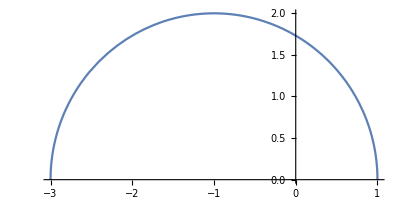

```mathematica
ParametricPlot[{1/8 (12-k^2),+1/8 √(-144+40 k^2-k^4)},{k,2,6},AspectRatio->Automatic]
```